## Time Independent Equations ESGB

```mathematica
odesys = {ss'[r]+(2 ss[r]^2 (1+8 (-1+ss[r]^2) Q'[r] β'[ϕ[r]])+Q[r]^2 (-1+ss[r]^2) (r^2+16 ss[r]^2 β''[ϕ[r]]))/(4 ss[r] (r+4 Q[r] (-2+3 ss[r]^2) β'[ϕ[r]])),nn'[r]-(nn[r] (8 ss[r]^2 Q'[r] β'[ϕ[r]]+Q[r]^2 (r^2+8 ss[r]^2 β''[ϕ[r]])))/(2 (r+4 Q[r] (-2+3 ss[r]^2) β'[ϕ[r]])),Q'[r]-(12 r ss[r]^4 β'[ϕ[r]]+Q[r] (2 r^4-r^4 ss[r]^2-96 ss[r]^4 β'[ϕ[r]]^2+96 ss[r]^6 β'[ϕ[r]]^2)+8 r^2 Q[r]^5 (-1+ss[r]^2)^2 β'[ϕ[r]]^2 (r^2+24 ss[r]^4 β''[ϕ[r]])-4 r Q[r]^2 β'[ϕ[r]] (12 r^2-25 r^2 ss[r]^2-24 ss[r]^6 β''[ϕ[r]]+12 ss[r]^4 (r^2+2 β''[ϕ[r]]))-r Q[r]^4 (-1+ss[r]^2) β'[ϕ[r]] (-r^4-1024 β'[ϕ[r]]^2+2880 ss[r]^6 β'[ϕ[r]]^2-48 ss[r]^4 (128 β'[ϕ[r]]^2+r^2 β''[ϕ[r]])+ss[r]^2 (r^4+4352 β'[ϕ[r]]^2+32 r^2 β''[ϕ[r]]))+4 Q[r]^3 (-1+ss[r]^2) (r^4 ss[r]^2 β''[ϕ[r]]-8 β'[ϕ[r]]^2 (12 r^2-32 r^2 ss[r]^2-24 ss[r]^6 β''[ϕ[r]]+3 ss[r]^4 (7 r^2+8 β''[ϕ[r]]))))/((-1+ss[r]^2) (r^5-96 r ss[r]^4 β'[ϕ[r]]^2+96 r^3 Q[r]^2 (2-5 ss[r]^2+3 ss[r]^4) β'[ϕ[r]]^2+64 r^2 Q[r]^3 (-8+32 ss[r]^2-39 ss[r]^4+15 ss[r]^6) β'[ϕ[r]]^3+4 Q[r] β'[ϕ[r]] (-6 r^4+7 r^4 ss[r]^2+192 ss[r]^4 β'[ϕ[r]]^2-192 ss[r]^6 β'[ϕ[r]]^2))),-Q[r]+ϕ'[r]};
```

```mathematica
odedecoupled = {Q'[r]+(12 r^3 rh^2 β'[ϕ[r]]+Q[r] (r^7 (2 r-rh)-96 r (r-rh) rh^2 β'[ϕ[r]]^2)+8 r^2 (r-rh)^2 Q[r]^5 β'[ϕ[r]]^2 (r^4+24 rh^2 β''[ϕ[r]])-4 r^2 Q[r]^2 β'[ϕ[r]] (r^3 (12 r^2-25 r rh+12 rh^2)+24 (r-rh) rh^2 β''[ϕ[r]])-r (r-rh) Q[r]^4 β'[ϕ[r]] (r^6 (r-rh)+64 (4 r-5 rh) (2 r-3 rh)^2 β'[ϕ[r]]^2+16 r^3 rh (-2 r+3 rh) β''[ϕ[r]])-4 (r-rh) Q[r]^3 (r^6 rh β''[ϕ[r]]-8 β'[ϕ[r]]^2 (r^3 (12 r^2-32 r rh+21 rh^2)+24 (r-rh) rh^2 β''[ϕ[r]])))/((r-rh) (r^8-4 r^6 (6 r-7 rh) Q[r] β'[ϕ[r]]-96 r^2 rh^2 β'[ϕ[r]]^2+96 r^4 (2 r^2-5 r rh+3 rh^2) Q[r]^2 β'[ϕ[r]]^2+768 (r-rh) rh^2 Q[r] β'[ϕ[r]]^3-64 r^2 (8 r^3-32 r^2 rh+39 r rh^2-15 rh^3) Q[r]^3 β'[ϕ[r]]^3)),
-Q[r]+ϕ'[r]};
```

```mathematica
odedecoupled/.{β-> Function[x,  ϵ*x],Q-> Function[r,ϕ'[r]]}//Simplify;
%[[1]];
Collect[%,{ϕ''[r], ϕ'[r], ϕ[r]}];
%/.{rh-> 1}//Simplify
```

(12 r^3 ϵ+(r^7 (-1+2 r)-96 (-1+r) r ϵ^2) ϕ'[r]-4 r^5 (12-25 r+12 r^2) ϵ ϕ'[r]^2+32 (-1+r) r^3 (21-32 r+12 r^2) ϵ^2 ϕ'[r]^3-(-1+r) r ϵ ((-1+r) r^6+64 (3-2 r)^2 (-5+4 r) ϵ^2) ϕ'[r]^4+8 (-1+r)^2 r^6 ϵ^2 ϕ'[r]^5)/((-1+r) (r^8-96 r^2 ϵ^2-4 r^6 (-7+6 r) ϵ ϕ'[r]+768 (-1+r) ϵ^3 ϕ'[r]+96 r^4 (3-5 r+2 r^2) ϵ^2 ϕ'[r]^2-64 r^2 (-15+39 r-32 r^2+8 r^3) ϵ^3 ϕ'[r]^3))+ϕ''[r]

```mathematica
DSolve[(12 r^3 rh^2 ϵ+(r^7 (2 r-rh)-96 r (r-rh) rh^2 ϵ^2) ϕ'[r]-4 r^5 (12 r^2-25 r rh+12 rh^2) ϵ ϕ'[r]^2+32 r^3 (r-rh) (12 r^2-32 r rh+21 rh^2) ϵ^2 ϕ'[r]^3-r (r-rh) ϵ (r^6 (r-rh)+64 (4 r-5 rh) (2 r-3 rh)^2 ϵ^2) ϕ'[r]^4+8 r^6 (r-rh)^2 ϵ^2 ϕ'[r]^5)/((r-rh) (r^8-96 r^2 rh^2 ϵ^2-4 r^6 (6 r-7 rh) ϵ ϕ'[r]+768 (r-rh) rh^2 ϵ^3 ϕ'[r]+96 r^4 (2 r^2-5 r rh+3 rh^2) ϵ^2 ϕ'[r]^2-64 r^2 (8 r^3-32 r^2 rh+39 r rh^2-15 rh^3) ϵ^3 ϕ'[r]^3))+ϕ''[r]==0,ϕ,r]
```

$Aborted

```mathematica
Normal@Series[%,{ϵ,0,1}]
```

((2 r-rh) ϕ'[r])/(r (r-rh))+(ϵ (12 rh^2+20 r^3 rh ϕ'[r]^2-20 r^2 rh^2 ϕ'[r]^2-r^6 ϕ'[r]^4+2 r^5 rh ϕ'[r]^4-r^4 rh^2 ϕ'[r]^4))/(r^5 (r-rh))+ϕ''[r]

```mathematica
rulehorizon = {nn-> Function[{r},Sum[ Subscript[nn, j](r-rh)^j, {j,0,4}]],
ss-> Function[{r}, 1 + Sum[Subscript[ss, j]*(r-rh)^j, {j,1,4}]],
ϕ -> Function[{r}, Sum[Subscript[ϕ, j]*(r-rh)^j,{j,0,4}]],
Q-> Function[{r}, D[Sum[Subscript[ϕ, j]*(r-rh)^j,{j,0,4}], r]]};
```

### Coefficients Near Horizon:

```mathematica
odesys/.rulehorizon;
Normal@Series[%,{r,rh,1}]/.coeffsrule[[1]]//Simplify;
%/.{Subscript[ϕ, 1]^2-> (-rh^3 Subscript[ϕ, 1]-12 β'[Subscript[ϕ, 0]])/(4 rh^2 β'[Subscript[ϕ, 0]])};
%//Simplify;
%/.{Subscript[ϕ, 2]-> (-80 rh^3 Subscript[ϕ, 1]^3 β'[Subscript[ϕ, 0]]^2-64 rh^2 Subscript[ϕ, 1]^4 β'[Subscript[ϕ, 0]]^3+12 β'[Subscript[ϕ, 0]] (7 rh^2-12 β''[Subscript[ϕ, 0]])+Subscript[ϕ, 1] (rh^5+48 rh β'[Subscript[ϕ, 0]]^2-24 rh^3 β''[Subscript[ϕ, 0]]))/(4 rh^2 (rh^4+4 rh^3 Subscript[ϕ, 1] β'[Subscript[ϕ, 0]]-96 β'[Subscript[ϕ, 0]]^2))}//Simplify;
%[[1]]
```

-1/(4 (rh+4 ϕ_1 β'[ϕ_0])^3)(r-rh) (-8 ss_2 (rh+4 ϕ_1 β'[ϕ_0])^3-(72 β''[ϕ_0])/rh+4 ϕ_1^3 β'[ϕ_0] (rh^2+24 β''[ϕ_0])+(12 β'[ϕ_0] (-80 rh^3 ϕ_1^3 β'[ϕ_0]^2-64 rh^2 ϕ_1^4 β'[ϕ_0]^3+12 β'[ϕ_0] (7 rh^2-12 β''[ϕ_0])+ϕ_1 (rh^5+48 rh β'[ϕ_0]^2-24 rh^3 β''[ϕ_0])))/(rh^5+4 rh^4 ϕ_1 β'[ϕ_0]-96 rh β'[ϕ_0]^2)-1/(4 β'[ϕ_0])ϕ_1 (rh^4+48 β'[ϕ_0]^2+24 rh^2 β''[ϕ_0]+(192 β'[ϕ_0]^3 (80 rh^3 ϕ_1^3 β'[ϕ_0]^2+64 rh^2 ϕ_1^4 β'[ϕ_0]^3+12 β'[ϕ_0] (-7 rh^2+12 β''[ϕ_0])-ϕ_1 (rh^5+48 rh β'[ϕ_0]^2-24 rh^3 β''[ϕ_0])))/(rh^6+4 rh^5 ϕ_1 β'[ϕ_0]-96 rh^2 β'[ϕ_0]^2)))

```mathematica
coeffsrule = {Subscript[ss, 1]->-1/(2 (rh+4 Subscript[ϕ, 1] β'[Subscript[ϕ, 0]])),
Subscript[ss, 2]->-((12288 rh^2 Subscript[ϕ, 1]^5 β'[Subscript[ϕ, 0]]^6-64 rh^3 Subscript[ϕ, 1]^4 β'[Subscript[ϕ, 0]]^3 (rh^4-288 β'[Subscript[ϕ, 0]]^2+24 rh^2 β''[Subscript[ϕ, 0]])+4 rh Subscript[ϕ, 1]^2 β'[Subscript[ϕ, 0]] (rh^4+48 β'[Subscript[ϕ, 0]]^2) (rh^4-48 β'[Subscript[ϕ, 0]]^2+24 rh^2 β''[Subscript[ϕ, 0]])+Subscript[ϕ, 1] (-96 rh^6 β'[Subscript[ϕ, 0]]^2-4608 β'[Subscript[ϕ, 0]]^4 (5 rh^2-6 β''[Subscript[ϕ, 0]])+rh^8 (rh^2+24 β''[Subscript[ϕ, 0]]))-16 rh^2 Subscript[ϕ, 1]^3 β'[Subscript[ϕ, 0]]^2 (rh^6+24 rh^4 β''[Subscript[ϕ, 0]]-48 β'[Subscript[ϕ, 0]]^2 (7 rh^2+48 β''[Subscript[ϕ, 0]]))+288 (rh^5 β'[Subscript[ϕ, 0]] β''[Subscript[ϕ, 0]]-2 β'[Subscript[ϕ, 0]]^3 (7 rh^3+36 rh β''[Subscript[ϕ, 0]])))/(32 rh^2 β'[Subscript[ϕ, 0]] (rh+4 Subscript[ϕ, 1] β'[Subscript[ϕ, 0]])^3 (rh^4+4 rh^3 Subscript[ϕ, 1] β'[Subscript[ϕ, 0]]-96 β'[Subscript[ϕ, 0]]^2))),
Subscript[ϕ, 1]->(-rh^3+√(rh^6-192 rh^2 β'[Subscript[ϕ, 0]]^2))/(8 rh^2 β'[Subscript[ϕ, 0]]),
Subscript[ϕ, 2]-> (-80 rh^3 Subscript[ϕ, 1]^3 β'[Subscript[ϕ, 0]]^2-64 rh^2 Subscript[ϕ, 1]^4 β'[Subscript[ϕ, 0]]^3+12 β'[Subscript[ϕ, 0]] (7 rh^2-12 β''[Subscript[ϕ, 0]])+Subscript[ϕ, 1] (rh^5+48 rh β'[Subscript[ϕ, 0]]^2-24 rh^3 β''[Subscript[ϕ, 0]]))/(4 rh^2 (rh^4+4 rh^3 Subscript[ϕ, 1] β'[Subscript[ϕ, 0]]-96 β'[Subscript[ϕ, 0]]^2))};
```

## Gaussian Theory

```mathematica
genseries[ϵ_,rh_,ϕ0_,μ_,l_ ]:= Module[{ϕ1,ϕ2,ss1,ss2,rulebeta,ϕmax},
rulebeta = {β-> Function[x, l^2*(1- Exp[-μ*x^2])/(2μ)]};
ϕ1 = (-rh^3+√(rh^6-192 rh^2 β'[ϕ0]^2))/(8 rh^2 β'[ϕ0])/.rulebeta;
ss1 = -1/(2 (rh+4 ϕ1 β'[ϕ0]))/.rulebeta;
ϕ2 = (-80 rh^3 ϕ1^3 β'[ϕ0]^2-64 rh^2 ϕ1^4 β'[ϕ0]^3+12 β'[ϕ0] (7 rh^2-12 β''[ϕ0])+ϕ1 (rh^5+48 rh β'[ϕ0]^2-24 rh^3 β''[ϕ0]))/(4 rh^2 (rh^4+4 rh^3 ϕ1 β'[ϕ0]-96 β'[ϕ0]^2)) /.rulebeta;
ss2 = -((12288 rh^2 ϕ1^5 β'[ϕ0]^6-64 rh^3 ϕ1^4 β'[ϕ0]^3 (rh^4-288 β'[ϕ0]^2+24 rh^2 β''[ϕ0])+4 rh ϕ1^2 β'[ϕ0] (rh^4+48 β'[ϕ0]^2) (rh^4-48 β'[ϕ0]^2+24 rh^2 β''[ϕ0])+ϕ1 (-96 rh^6 β'[ϕ0]^2-4608 β'[ϕ0]^4 (5 rh^2-6 β''[ϕ0])+rh^8 (rh^2+24 β''[ϕ0]))-16 rh^2 ϕ1^3 β'[ϕ0]^2 (rh^6+24 rh^4 β''[ϕ0]-48 β'[ϕ0]^2 (7 rh^2+48 β''[ϕ0]))+288 (rh^5 β'[ϕ0] β''[ϕ0]-2 β'[ϕ0]^3 (7 rh^3+36 rh β''[ϕ0])))/(32 rh^2 β'[ϕ0] (rh+4 ϕ1 β'[ϕ0])^3 (rh^4+4 rh^3 ϕ1 β'[ϕ0]-96 β'[ϕ0]^2))) /.rulebeta;
{1 + ss1*ϵ + ss2*ϵ^2, ϕ1 + 2*(ϵ)*ϕ2, ϕ0 + ϵ*ϕ1 + ϵ^2*ϕ2}]
```

```mathematica
genseriesdecoupled[ϵ_,rh_,ϕ0_,μ_,l_]:= Module[{ϕ1,ϕ2,rulebeta},
rulebeta = {β-> Function[x, l^2*(1- Exp[-μ*x^2])/(2μ)]};
ϕ1 = (-rh^3+√(rh^6-192 rh^2 β'[ϕ0]^2))/(8 rh^2 β'[ϕ0])/.rulebeta;
ϕ2 = (-80 rh^3 ϕ1^3 β'[ϕ0]^2-64 rh^2 ϕ1^4 β'[ϕ0]^3+12 β'[ϕ0] (7 rh^2-12 β''[ϕ0])+ϕ1 (rh^5+48 rh β'[ϕ0]^2-24 rh^3 β''[ϕ0]))/(4 rh^2 (rh^4+4 rh^3 ϕ1 β'[ϕ0]-96 β'[ϕ0]^2)) /.rulebeta;
{ϕ1 + 2*(ϵ)*ϕ2, ϕ0 + ϵ*ϕ1 + ϵ^2*ϕ2}]
```

```mathematica
genseriesdecoupled1[ϵ_,rh_,ϕ0_,μ_,l_]:= Module[{ϕ1,ϕ2,rulebeta},
rulebeta = {β-> Function[x, l^2*(1- Exp[-μ*x^2])/(2μ)]};
ϕ1 = -(12 β'[ϕ0])/rh^3/.rulebeta;
{ϕ1 , ϕ0 + ϵ*ϕ1 }]
```

```mathematica
odesoldecoupled[ϕ0_?NumericQ,μ_?NumericQ, l_?NumericQ,rh_?NumericQ,rend_?NumericQ]:= Module[{ϵ,ssval,Qval,phival,valshorizon,ndsol},
ϵ = 10^-6;
If[1-192 ⅇ^(-2 μ ϕ0^2) l^4 ϕ0^2<=0, Print["Kanti bound exceeded"] ,
valshorizon = genseriesdecoupled[ϵ,rh,ϕ0,μ,l]; 
Qval = valshorizon[[1]];
phival = valshorizon[[2]];
ndsol = NDSolve[{(ⅇ^(3 μ ϕ[r]^2) (12 ⅇ^(-μ ϕ[r]^2) l^2 r^3 rh^2 ϕ[r]+Q[r] (r^7 (2 r-rh)-96 ⅇ^(-2 μ ϕ[r]^2) l^4 r (r-rh) rh^2 ϕ[r]^2)+8 ⅇ^(-3 μ ϕ[r]^2) l^4 r^2 (r-rh)^2 Q[r]^5 ϕ[r]^2 (ⅇ^(μ ϕ[r]^2) r^4+24 l^2 rh^2-48 l^2 rh^2 μ ϕ[r]^2)+4 ⅇ^(-2 μ ϕ[r]^2) l^2 r^2 Q[r]^2 ϕ[r] (24 l^2 rh^2 (-r+rh)-ⅇ^(μ ϕ[r]^2) r^3 (12 r^2-25 r rh+12 rh^2)+48 l^2 (r-rh) rh^2 μ ϕ[r]^2)+4 ⅇ^(-3 μ ϕ[r]^2) l^2 (r-rh) Q[r]^3 (-ⅇ^(2 μ ϕ[r]^2) r^6 rh+2 (96 l^4 (r-rh) rh^2+4 ⅇ^(μ ϕ[r]^2) l^2 r^3 (12 r^2-32 r rh+21 rh^2)+ⅇ^(2 μ ϕ[r]^2) r^6 rh μ) ϕ[r]^2-384 l^4 (r-rh) rh^2 μ ϕ[r]^4)-ⅇ^(-μ ϕ[r]^2) l^2 r (r-rh) Q[r]^4 ϕ[r] (r^6 (r-rh)+64 ⅇ^(-2 μ ϕ[r]^2) l^4 (4 r-5 rh) (2 r-3 rh)^2 ϕ[r]^2+16 ⅇ^(-μ ϕ[r]^2) l^2 r^3 (2 r-3 rh) rh (-1+2 μ ϕ[r]^2))))/((r-rh) (ⅇ^(3 μ ϕ[r]^2) r^8-4 ⅇ^(2 μ ϕ[r]^2) l^2 r^6 (6 r-7 rh) Q[r] ϕ[r]-96 ⅇ^(μ ϕ[r]^2) l^4 r^2 rh^2 ϕ[r]^2+96 ⅇ^(μ ϕ[r]^2) l^4 r^4 (2 r^2-5 r rh+3 rh^2) Q[r]^2 ϕ[r]^2+768 l^6 (r-rh) rh^2 Q[r] ϕ[r]^3-64 l^6 r^2 (8 r^3-32 r^2 rh+39 r rh^2-15 rh^3) Q[r]^3 ϕ[r]^3))+Q'[r]==0,-Q[r]+ϕ'[r]==0,
Q[rh + ϵ] == Qval,
ϕ[rh + ϵ]==phival},
{Q,ϕ},{r, rh + ϵ, rend},AccuracyGoal->15,PrecisionGoal->15, Method->{"StiffnessSwitching","NonstiffTest"->False}];
ndsol[[1]] ]]
```

```mathematica
odesoldecoupled1[ϕ0_?NumericQ,μ_?NumericQ, l_?NumericQ,rh_?NumericQ,rend_?NumericQ]:= Module[{ϵ,ssval,Qval,phival,valshorizon,ndsol},
ϵ = 10^-6;
If[1-192 ⅇ^(-2 μ ϕ0^2) l^4 ϕ0^2<=0, Print["Kanti bound exceeded"] ,
valshorizon = genseriesdecoupled1[ϵ,rh,ϕ0,μ,l]; 
Qval = valshorizon[[1]];
phival = valshorizon[[2]];
ndsol = NDSolve[{Q'[r]==-(ⅇ^(-μ ϕ[r]^2) (2 ⅇ^(μ ϕ[r]^2) r^5 Q[r]-ⅇ^(μ ϕ[r]^2) r^4 rh Q[r]+12 l^2 rh^2 ϕ[r]))/(r^5 (r-rh)),-Q[r]+ϕ'[r]==0,
Q[rh + ϵ] == Qval,
ϕ[rh + ϵ]==phival},
{Q,ϕ},{r, rh + ϵ, rend},AccuracyGoal->15,PrecisionGoal->15, Method->{"StiffnessSwitching","NonstiffTest"->False}];
ndsol[[1]] ]]
```

```mathematica
odesol[ϕ0_?NumericQ,μ_?NumericQ, l_?NumericQ,rh_?NumericQ,rend_?NumericQ]:= Module[{ϵ,ssval,Qval,phival,valshorizon,ndsol},
ϵ = 10^-6;
If[rh^4-192 ⅇ^(-2 μ ϕ0^2) l^4 ϕ0^2<=0, Print["Kanti bound exceeded"] ,
valshorizon = genseries[ϵ,rh,ϕ0,μ,l];
ssval = valshorizon[[1]]; 
Qval = valshorizon[[2]];
phival = valshorizon[[3]];
ndsol = NDSolve[{(Q[r]^2 (-1+ss[r]^2) (ⅇ^(μ ϕ[r]^2) r^2+16 l^2 ss[r]^2 (1-2 μ ϕ[r]^2))+2 ss[r]^2 (ⅇ^(μ ϕ[r]^2)+8 l^2 (-1+ss[r]^2) ϕ[r] Q'[r]))/(4 ss[r] (ⅇ^(μ ϕ[r]^2) r+4 l^2 Q[r] (-2+3 ss[r]^2) ϕ[r]))+ss'[r] ==0,
(-12 ⅇ^(2 μ ϕ[r]^2) l^2 r ss[r]^4 ϕ[r]+ⅇ^(μ ϕ[r]^2) Q[r] (-2 ⅇ^(2 μ ϕ[r]^2) r^4+ⅇ^(2 μ ϕ[r]^2) r^4 ss[r]^2+96 l^4 ss[r]^4 ϕ[r]^2-96 l^4 ss[r]^6 ϕ[r]^2)-8 l^4 r^2 Q[r]^5 (-1+ss[r]^2)^2 ϕ[r]^2 (ⅇ^(μ ϕ[r]^2) r^2+24 l^2 ss[r]^4 (1-2 μ ϕ[r]^2))+4 ⅇ^(μ ϕ[r]^2) l^2 r Q[r]^2 ϕ[r] (12 ⅇ^(μ ϕ[r]^2) r^2-25 ⅇ^(μ ϕ[r]^2) r^2 ss[r]^2+24 l^2 ss[r]^6 (-1+2 μ ϕ[r]^2)+12 ss[r]^4 (2 l^2+ⅇ^(μ ϕ[r]^2) r^2-4 l^2 μ ϕ[r]^2))+l^2 r Q[r]^4 (-1+ss[r]^2) ϕ[r] (-ⅇ^(2 μ ϕ[r]^2) r^4-1024 l^4 ϕ[r]^2+2880 l^4 ss[r]^6 ϕ[r]^2-48 l^2 ss[r]^4 (ⅇ^(μ ϕ[r]^2) r^2+2 (64 l^2-ⅇ^(μ ϕ[r]^2) r^2 μ) ϕ[r]^2)+ss[r]^2 (ⅇ^(μ ϕ[r]^2) r^2 (32 l^2+ⅇ^(μ ϕ[r]^2) r^2)+64 l^2 (68 l^2-ⅇ^(μ ϕ[r]^2) r^2 μ) ϕ[r]^2))+4 l^2 Q[r]^3 (-1+ss[r]^2) (96 ⅇ^(μ ϕ[r]^2) l^2 r^2 ϕ[r]^2+192 l^4 ss[r]^6 ϕ[r]^2 (-1+2 μ ϕ[r]^2)-24 l^2 ss[r]^4 ϕ[r]^2 (-8 l^2-7 ⅇ^(μ ϕ[r]^2) r^2+16 l^2 μ ϕ[r]^2)+ⅇ^(μ ϕ[r]^2) r^2 ss[r]^2 (-ⅇ^(μ ϕ[r]^2) r^2+(-256 l^2+2 ⅇ^(μ ϕ[r]^2) r^2 μ) ϕ[r]^2)))/((-1+ss[r]^2) (ⅇ^(3 μ ϕ[r]^2) r^5-96 ⅇ^(μ ϕ[r]^2) l^4 r ss[r]^4 ϕ[r]^2+96 ⅇ^(μ ϕ[r]^2) l^4 r^3 Q[r]^2 (2-5 ss[r]^2+3 ss[r]^4) ϕ[r]^2+64 l^6 r^2 Q[r]^3 (-8+32 ss[r]^2-39 ss[r]^4+15 ss[r]^6) ϕ[r]^3+4 l^2 Q[r] ϕ[r] (-6 ⅇ^(2 μ ϕ[r]^2) r^4+7 ⅇ^(2 μ ϕ[r]^2) r^4 ss[r]^2+192 l^4 ss[r]^4 ϕ[r]^2-192 l^4 ss[r]^6 ϕ[r]^2)))+Q'[r] ==0,
-Q[r]+ϕ'[r] ==0 , 
ss[rh + ϵ]== ssval,
Q[rh + ϵ] == Qval,
ϕ[rh + ϵ]==phival},
{ss,Q,ϕ},{r, rh + ϵ, rend},AccuracyGoal->15,PrecisionGoal->15, Method->{"StiffnessSwitching","NonstiffTest"->False}];
ndsol[[1]] ]]
```

```mathematica
plotsodevsdecoupled[ϕ0_?NumericQ, l_?NumericQ,μ_?NumericQ]:= Module[{rh,rend,expr1,expr2,p1,p2,p3,p4,expr0},
rh = 1; 
rend = 10^5; 
expr0 = odesoldecoupled1[ϕ0,μ,l,rh,rend];
expr1 = odesoldecoupled[ϕ0,μ,l,rh,rend];
expr2 = odesol[ϕ0,μ,l,rh,rend];
p1 = Plot[{ϕ[r]/.expr0,ϕ[r]/.expr1,ϕ[r]/.expr2},{r,1,100},PlotRange->All,Frame->True,PlotLegends->{"Schwarzschild","Decoupled","Exact"},ImageSize->Medium,FrameLabel->{"r","ϕ[r]"}];
p2 = LogLogPlot[{Abs[(ϕ[r]/.expr2)- (ϕ[r]/.expr1)],Abs[(ϕ[r]/.expr2)- (ϕ[r]/.expr0)]},{r,1,100},PlotRange->{{1,100},All},Frame->True,ImageSize->Medium,PlotLegends->{"Decoup-Exact","GR-Exact"}];
p3 = LogLogPlot[{Abs[-r^2*Derivative[1][ϕ][r]/.expr0],Abs[-r^2*Derivative[1][ϕ][r]/.expr1],Abs[-r^2*Derivative[1][ϕ][r]/.expr2]},{r,1,100},PlotRange->All,Frame->True,PlotLegends->{"Schwarzschild","Decoupled","Exact"},ImageSize->Medium];
p4 = LogLogPlot[{Abs[(Derivative[1][ϕ][r]/.expr2)- (Derivative[1][ϕ][r]/.expr1)],Abs[(Derivative[1][ϕ][r]/.expr2)- (Derivative[1][ϕ][r]/.expr0)]},{r,1,100},PlotRange->{{1,100},All},Frame->True,ImageSize->Medium,PlotLegends->{"Decoup-Exact","GR-Exact"}];
{p1,p2,p3,p4}]
```

```mathematica
asymvals[ϕ0_?NumericQ,μ_?NumericQ, l_?NumericQ,rh_?NumericQ,rend_?NumericQ]:=( 
If[rh^4-192 ⅇ^(-2 μ ϕ0^2) l^4 ϕ0^2<=0,(* Print["Kanti bound exceeded"];*) {-1,-1,-20} ,{ss[rend]^2*rend/2, ϕ[rend],-rend*rend*Derivative[1][ϕ][rend]}/.odesol[ϕ0,μ,l,rh,rend]])
```

```mathematica
asymvalsdecoupled[ϕ0_?NumericQ,μ_?NumericQ, l_?NumericQ,rh_?NumericQ,rend_?NumericQ]:= ( 
If[rh^4-192 ⅇ^(-2 μ ϕ0^2) l^4 ϕ0^2<=0,(* Print["Kanti bound exceeded"];*) {-1,-1,-20} ,{0.5*rh, ϕ[rend],-rend*rend*Derivative[1][ϕ][rend]}/.odesoldecoupled[ϕ0,μ,l,rh,rend]])
```

```mathematica
phivals =DeleteDuplicates@Join[Subdivide[10^-6,10^-3,10],Subdivide[10^-3,0.1,100],Subdivide[0.1,1,1000]] //N;
```

```mathematica
mylist[l_,rh_] := Table[Join[{phivals[[j]]} ,asymvals[phivals[[j]],3,l,rh,10^10*rh]],{j,1,Length[phivals]}];
```

```mathematica
mylistdecoupled[l_,rh_]:=  Table[Join[{phivals[[j]]} ,asymvalsdecoupled[phivals[[j]],3,l,rh,10^10*rh]],{j,1,Length[phivals]}];
```

```mathematica
asymvDD[l_,rh_,phi0_]:= asymvals[phi0,3,l,rh,rh*10^5]
```

```mathematica
getplot[l_,μ_,color_]:= Module[{list$},
rh=1;
list$ = Table[Join[{phivals[[j]]} ,asymvals[phivals[[j]],μ,l,rh,10^5*rh]],{j,1,Length[phivals]}];
p1 = ListLogPlot[Table[{list$[[All,1]][[j]],Abs[list$[[All,3]][[j]]]},{j,1,Length[list$]}],PlotRange->All,Frame->True,PlotLegends->{"μ = "<>ToString[μ]<>"; l = "<>ToString[l]}, PlotStyle->{PointSize[0.01],color},FrameLabel->{"ϕ_H","Log[ϕ_asym]"},LabelStyle->{Directive[Bold, Medium],Black},ImageSize->Medium];
p2 = ListLogPlot[Table[{list$[[All,1]][[j]],Abs[list$[[All,4]][[j]]]},{j,1,Length[list$]}],PlotRange->All,Frame->True,PlotLegends->{"μ = "<>ToString[μ]<>"; l = "<>ToString[l]}, PlotStyle->{PointSize[0.01],color},FrameLabel->{"ϕ_H","Log[Q]"},LabelStyle->{Directive[Bold, Medium],Black},ImageSize->Medium];
{p1,p2}]
getplotdecoupled[l_,μ_,color_]:= Module[{list$},
rh=1;
list$ = Table[Join[{phivals[[j]]} ,asymvalsdecoupled[phivals[[j]],μ,l,rh,10^10*rh]],{j,1,Length[phivals]}];
p1 = ListLogPlot[Table[{list$[[All,1]][[j]],Abs[list$[[All,3]][[j]]]},{j,1,Length[list$]}],PlotRange->All,Frame->True,PlotLegends->{"μ = "<>ToString[μ]<>"; l = "<>ToString[l]}, PlotStyle->{PointSize[0.01],color},FrameLabel->{"ϕ_H","Log[ϕ_asym]"},LabelStyle->{Directive[Bold, Medium],Black},ImageSize->Medium];
p2 = ListLogPlot[Table[{list$[[All,1]][[j]],Abs[list$[[All,4]][[j]]]},{j,1,Length[list$]}],PlotRange->All,Frame->True,PlotLegends->{"μ = "<>ToString[μ]<>"; l = "<>ToString[l]}, PlotStyle->{PointSize[0.01],color},FrameLabel->{"ϕ_H","Log[Q]"},LabelStyle->{Directive[Bold, Medium],Black},ImageSize->Medium];
{p1,p2}]
```

```mathematica
list1[μ_,l_] := Table[Join[{phivals[[j]]} ,asymvalsdecoupled[phivals[[j]],μ,l,rh,10^10*rh]],{j,1,Length[phivals]}];
```

```mathematica
list2[μ_,l_] := Table[Join[{phivals[[j]]} ,asymvals[phivals[[j]],μ,l,rh,10^10*rh]],{j,1,Length[phivals]}];
```

```mathematica
plotcomp[mu_,l_]:=Module[{l1,l2},
l1 = list1[mu,l];
l2 = list2[mu,l];
{ListLogPlot[Table[{l1[[All,1]][[j]], Abs[1- (l1[[All,1]][[j]])/(l2[[All,1]][[j]])]},{j,1,Length[l1]}],Frame->True],
ListLogPlot[Table[{l1[[All,1]][[j]], Abs[1- (l1[[All,2]][[j]])/(l2[[All,2]][[j]])]},{j,1,Length[l1]}],Frame->True],
ListLogPlot[Table[{l1[[All,1]][[j]], Abs[1- (l1[[All,3]][[j]])/(l2[[All,3]][[j]])]},{j,1,Length[l1]}],Frame->True]}]
```

```mathematica
getplotfull[l_,μ_,rh_,color_]:= Module[{list$},
list$ = Table[Join[{phivals[[j]]} ,asymvals[phivals[[j]],μ,l,rh,10^5*rh]],{j,1,Length[phivals]}];
p1 = ListLogPlot[Table[{list$[[All,1]][[j]],Abs[list$[[All,3]][[j]]]},{j,1,Length[list$]}],PlotRange->All,Frame->True,PlotLegends->{"μ = "<>ToString[μ]<>"; l = "<>ToString[l]}, PlotStyle->{PointSize[0.01],color},FrameLabel->{"ϕ_H","Log[ϕ_asym]"},LabelStyle->{Directive[Bold, Medium],Black},ImageSize->Medium];
p2 = ListLogPlot[Table[{list$[[All,1]][[j]],Abs[list$[[All,4]][[j]]]},{j,1,Length[list$]}],PlotRange->All,Frame->True,PlotLegends->{"μ = "<>ToString[μ]<>"; l = "<>ToString[l]}, PlotStyle->{PointSize[0.01],color},FrameLabel->{"ϕ_H","Log[Q]"},LabelStyle->{Directive[Bold, Medium],Black},ImageSize->Medium];
{p1,p2}]
```

## Analysis

```mathematica
odesol[ϕ0_?NumericQ,μ_?NumericQ, l_?NumericQ,rh_?NumericQ,rend_?NumericQ]
```

```mathematica
ans
```

odesol[0.45,12,0.5,0.58]

```mathematica
compareGR[ l_,mu_,ϕ0_,mh_]:=Module[{rh,p1,p2,p3},
rh = 2*mh; 
ans = odesol[ϕ0,mu,l,rh,rh*10^5];
p1 = LogLogPlot[{ss[r]/.ans, √(2*mh/r)},{r,rh,100},PlotRange->All,PlotLegends->{"Exact","GR"},ImageSize->Medium,Frame->True,FrameLabel->{"r","Shift profile"}];
p2=Plot[{Abs[(1- (√(2*mh/r))/(ss[r]/.ans))]*100,Abs[(1- mh/(r*ss[r]^2/2/.ans))]*100},{r,rh,100},PlotRange->All,ImageSize->Medium,Frame->True, FrameLabel->{"r","Percent difference"},PlotLegends->{"Profile","ADM Mass"}];
p3 = Plot[ϕ[r]/.ans, {r,rh,100},PlotRange->All,ImageSize->Medium,Frame->True, FrameLabel->{"r","ϕ[r]"}];

{p1,p2,p3}]
```

```mathematica
0.5*2.6
```

1.3

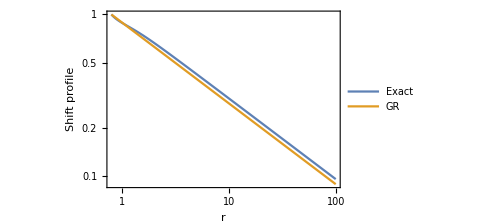
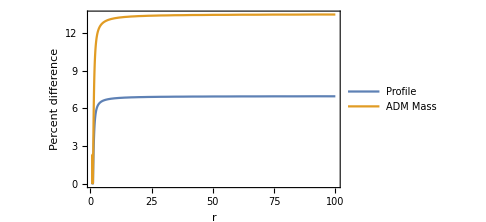
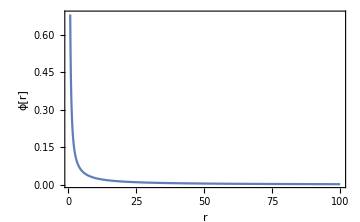

```mathematica
compareGR[0.5,3,0.68,0.4]
```

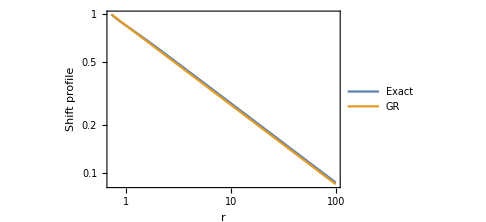
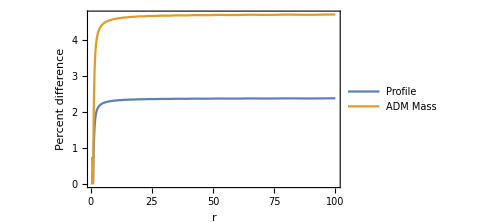
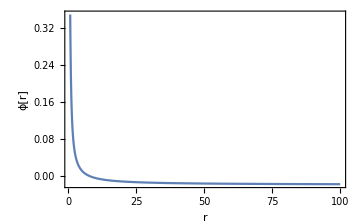

```mathematica
compareGR[0.5,12,0.35,0.36]
```

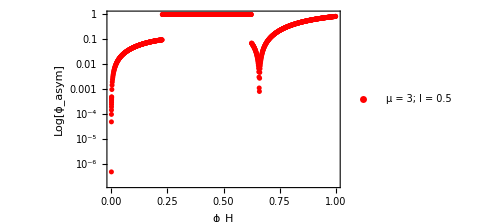
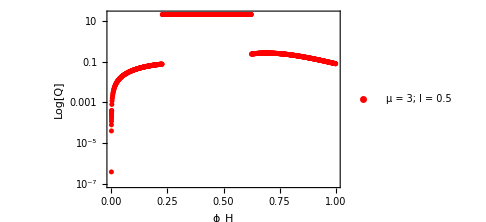

```mathematica
getplotfull[0.5,3,0.41*2,Red]
```

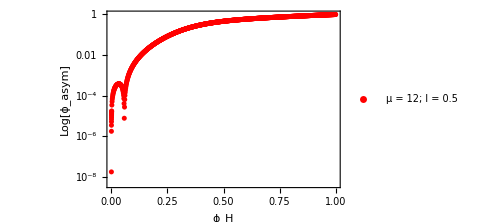
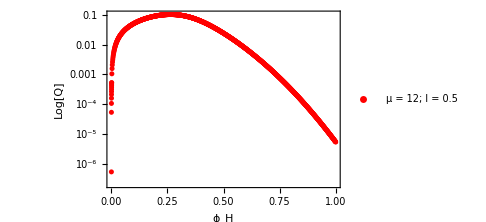

```mathematica
getplotfull[0.5,12,0.58*2,Red]
```

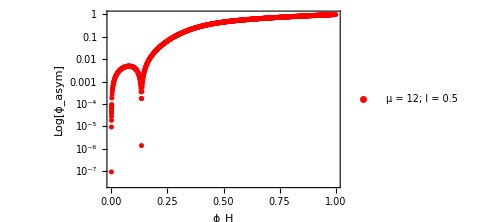
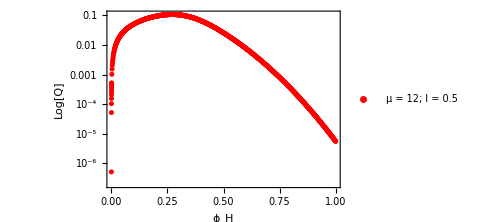

```mathematica
getplotfull[0.5,12,0.55*2,Red]
```

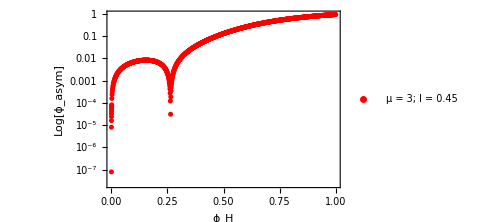
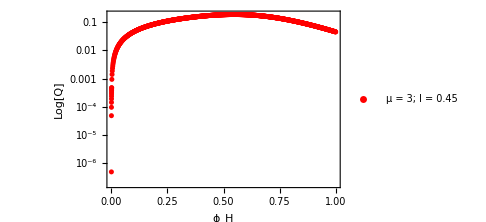

```mathematica
getplot[0.45,3,Red]
```

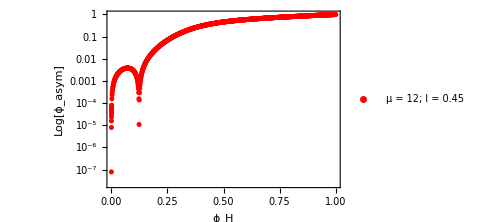
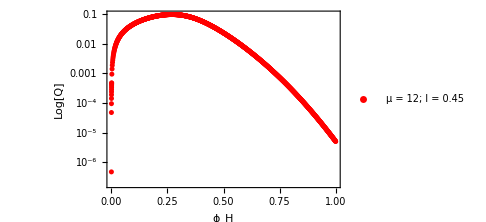

```mathematica
getplot[0.45,12,Red]
```

## Reproducing Hector:

### Reproducing Hector’s Plot:

Fig 12 of  "https://arxiv.org/pdf/2202.01329.pdf", Conversions, ϕ_J = ϕ_me/(√2), l_J = 2*l_me.

```mathematica
ls = {√(0.7/4),√(1./4), √(1.56/4), √(2.78/4),√(4.58/4)};
```

```mathematica
cs = {RGBColor[1,0,0],RGBColor[0,1,0.5],RGBColor[0,0,1],RGBColor[0.1,0.5,0],Yellow}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0.5],RGBColor[0, 0, 1],RGBColor[0.1, 0.5, 0],RGBColor[1, 1, 0]}

NDSolve::ndsz: At r == 1.00261, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {10000000000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {10000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {10000000000} and/or the interpolation grid is insufficient to compute the value.

NDSolve::ndsz: At r == 1.00644, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {10000000000} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

NDSolve::ndsz: At r == 1.01131, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

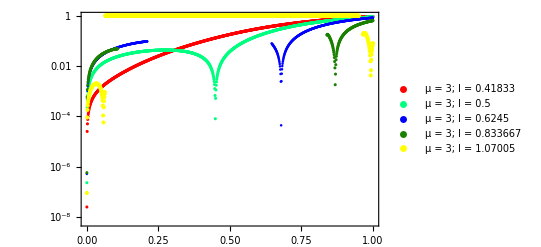

```mathematica
Show[Flatten@Table[getplot[ls[[j]],3,cs[[j]]],{j,1,Length[ls]}]]
```